```mathematica
Clear["Global`*"]
```

# Discrete-time matching alleles coevolution with two-patch model

```mathematica
WH1[1,u_,t_]:=pP[u,t](1-V) +(1-pP[u,t])S +(1-pP[u,t])(1-S)(1-V)
WH1[2,u_,t_]:=(1-pP[u,t])(1-V)+pP[u,t]S +pP[u,t](1-S)(1-V) 
WP1[1,u_,t_]:=pH[u,t]+(1-pH[u,t])(1-S)
WP1[2,u_,t_]:=(1-pH[u,t])+pH[u,t](1-S)
```

```mathematica
pH1[u_,t_]:=(pH[u,t] WH1[1,u,t])/(pH[u,t]WH1[1,u,t]+(1-pH[u,t])WH1[2,u,t])
pP1[u_,t_]:=(pP[u,t] WP1[1,u,t])/(pP[u,t]WP1[1,u,t]+(1-pP[u,t])WP1[2,u,t])
```

```mathematica
pH2[u_,t_]:=pH1[u,t](1-mH )+mH*pH1[Mod[u,2]+1,t]
pP2[u_,t_]:=pP1[u,t](1-mP)+mP*pP1[Mod[u,2]+1,t]
```

### Numerical time series

```mathematica
inits1={i1-> 0.495,i2-> 0.5,i3-> 0.5,i4-> 0.5};
pars1={p1-> 0.4117647058823529,p2-> 0.2200911052505395,p3-> 0.01,p4-> 0.01};
pars2={p1-> 0.3939393939393939,p2-> 0.4368677407268642,p3->0.01,p4-> 0.01};
pars3={p1-> 0.37500000000000006,p2-> 0.9004329004329,p3-> 0.01,p4-> 0.01};
```

```mathematica
Clear[timeSeries]
timeSeries[pars_,inits_,tmax_]:=timeSeries[pars,inits,tmax]=Block[
{WH1,WP1,pH1,pP1,pH2,pP2,S,V,mH,mP,pP,pH,i1,i2,i3,i4,p1,p2,p3,p4,out},

S=p1/.pars;
V=p2/.pars;
mH=p3/.pars;
mP=p4/.pars;

WH1[1,u_,t_]:=pP[u,t](1-V) +(1-pP[u,t])S +(1-pP[u,t])(1-S)(1-V);
WH1[2,u_,t_]:=(1-pP[u,t])(1-V)+pP[u,t]S +pP[u,t](1-S)(1-V) ;
WP1[1,u_,t_]:=pH[u,t]+(1-pH[u,t])(1-S);
WP1[2,u_,t_]:=(1-pH[u,t])+pH[u,t](1-S);

pH1[u_,t_]:=pH1[u,t]=((pH[u,t] WH1[1,u,t])/(pH[u,t]WH1[1,u,t]+(1-pH[u,t])WH1[2,u,t]));
pP1[u_,t_]:=pP1[u,t]=((pP[u,t] WP1[1,u,t])/(pP[u,t]WP1[1,u,t]+(1-pP[u,t])WP1[2,u,t]));

pH2[u_,t_]:=pH2[u,t]=pH1[u,t](1-mH )+mH*pH1[Mod[u,2]+1,t];pP2[u_,t_]:=pP2[u,t]=pP1[u,t](1-mP)+mP*pP1[Mod[u,2]+1,t];

pH[u_,t_]:=pH[u,t]=pH2[u,t-1];
pP[u_,t_]:=pP[u,t]=pP2[u,t-1];

pH[1,0]=i1/.inits;
pH[2,0]=i2/.inits;
pP[1,0]=i3/.inits;
pP[2,0]=i4/.inits;

out={Table[j,{j,0,tmax}],
Table[pH[1,j],{j,0,tmax}],
Table[pH[2,j],{j,0,tmax}],
Table[pP[1,j],{j,0,tmax}],
Table[pP[2,j],{j,0,tmax}]}
]
```

```mathematica
maxT=1000
```

1000

```mathematica
timeSeries[pars3,inits1,maxT][[4]]+timeSeries[pars3,inits1,maxT][[5]]//Length
```

101

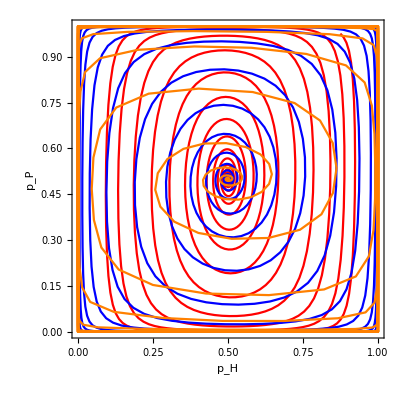

```mathematica
g=Show[ListLinePlot[Partition[Riffle[
(timeSeries[pars1,inits1,maxT][[2]]+timeSeries[pars1,inits1,maxT][[3]])/2,(timeSeries[pars1,inits1,maxT][[4]]+timeSeries[pars1,inits1,maxT][[5]])/2],2],AspectRatio-> 1,Frame-> True,FrameLabel-> {"p_H","p_P"},PlotRange-> {{0,1},{0,1}},PlotStyle-> Red],
ListLinePlot[Partition[Riffle[
(timeSeries[pars2,inits1,maxT][[2]]+timeSeries[pars2,inits1,maxT][[3]])/2,(timeSeries[pars2,inits1,maxT][[4]]+timeSeries[pars2,inits1,maxT][[5]])/2],2],AspectRatio-> 1,Frame-> True,FrameLabel-> {"p_H","p_P"},PlotRange-> {{0,1},{0,1}},PlotStyle-> Blue],
ListLinePlot[Partition[Riffle[
(timeSeries[pars3,inits1,maxT][[2]]+timeSeries[pars3,inits1,maxT][[3]])/2,(timeSeries[pars3,inits1,maxT][[4]]+timeSeries[pars3,inits1,maxT][[5]])/2],2],AspectRatio-> 1,Frame-> True,FrameLabel-> {"p_H","p_P"},PlotRange-> {{0,1},{0,1}},PlotStyle-> Orange]]
```

```mathematica
Export["~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Phase.png",g,ImageResolution-> 300]
```

~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Phase.png

### Equilibria

```mathematica
equs={pH2[1,t],pH2[2,t],pP2[1,t],pP2[2,t]};
```

```mathematica
equs3=Map[Simplify[Series[#/.{mH->ϵ μH,mP->ϵ μP},{ϵ,0,2}],Assumptions->{S>0,V>0,μH>0,μP>0,ϵ>0}]&,equs];
```

```mathematica
equi=Solve[equs3=={pH[1,t],pH[2,t],pP[1,t],pP[2,t]},{pH[1,t],pH[2,t],pP[1,t],pP[2,t]}]
```

{{pH[1,t]→0,pH[2,t]→0,pP[1,t]→0,pP[2,t]→0},{pH[1,t]→0,pH[2,t]→0,pP[1,t]→1,pP[2,t]→1},{pH[1,t]→1/2,pH[2,t]→1/2,pP[1,t]→1/2,pP[2,t]→1/2},{pH[1,t]→1,pH[2,t]→1,pP[1,t]→0,pP[2,t]→0},{pH[1,t]→1,pH[2,t]→1,pP[1,t]→1,pP[2,t]→1}}

### Stability

```mathematica
JMtrx={
{D[pH2[1,t],pH[1,t]],D[pH2[1,t],pH[2,t]],D[pH2[1,t],pP[1,t]],D[pH2[1,t],pP[2,t]]},{D[pH2[2,t],pH[1,t]],D[pH2[2,t],pH[2,t]],D[pH2[2,t],pP[1,t]],D[pH2[2,t],pP[2,t]]},
{D[pP2[1,t],pH[1,t]],D[pP2[1,t],pH[2,t]],D[pP2[1,t],pP[1,t]],D[pP2[1,t],pP[2,t]]},
{D[pP2[2,t],pH[1,t]],D[pP2[2,t],pH[2,t]],D[pP2[2,t],pP[1,t]],D[pP2[2,t],pP[2,t]]}};
```

```mathematica
Clear[JMtrxEqui,λList]
JMtrxEqui[e_]:=JMtrx/.equi[[e]]//Simplify;
λList[e_]:=JMtrxEqui[e]//Eigenvalues//FullSimplify;
```

#### Equilibrium 1 – all fixed for WT allele

```mathematica
JMtrxEqui[1]//MatrixForm
```

(((-1+mH) (1+(-1+S) V))/(-1+V) | -(mH (1+(-1+S) V))/(-1+V) | 0 | 0
-(mH (1+(-1+S) V))/(-1+V) | ((-1+mH) (1+(-1+S) V))/(-1+V) | 0 | 0
0 | 0 | (-1+mP) (-1+S) | mP-mP S
0 | 0 | mP-mP S | (-1+mP) (-1+S))

```mathematica
λList[1]
```

{(-1+2 mP) (-1+S),(-1+V-S V)/(-1+V),1-S,((-1+2 mH) (1+(-1+S) V))/(-1+V)}

```mathematica
Map[Simplify[#,Assumptions->{mH>0,mP>0,1>S>0,0<V<1}]&,λList[1]]
```

{(-1+2 mP) (-1+S),(-1+V-S V)/(-1+V),1-S,((-1+2 mH) (1+(-1+S) V))/(-1+V)}

```mathematica
Map[Reduce[{#>1,1≥ mP≥0,1≥ mH≥0,1>S>0,0<V<1}]&,λList[1]]//MatrixForm
```

(False
0≤mP≤1&&0<V<1&&0<S<1&&0≤mH≤1
False
0≤mP≤1&&0<S<1&&0≤mH<1/2&&-(2 mH)/(-2 mH-S+2 mH S)<V<1)

With some degree of virulence and specificity, always unstable.

```mathematica
Map[Reduce[{#<-1,1≥ mP≥0,1≥ mH≥0,1>S>0,0<V<1}]&,λList[1]]//MatrixForm
```

(False
False
False
0≤mP≤1&&0<S<1&&1/2<mH≤1&&(2-2 mH)/(2-2 mH-S+2 mH S)<V<1)

```mathematica
{{Eigenvalue, Conditions, Unique conditions}, {(-1+V-S V)/(-1+V), 0≤mP≤1&&0<V<1&&0<S<1&&0≤mH≤1, 0≤mH≤1,0<V<1}, {((-1+2 mH) (1+(-1+S) V))/(-1+V), 0≤mP≤1&&0<S<1&&1/2<mH≤1&&(2-2 mH)/(2-2 mH-S+2 mH S)<V<1, 1/2<mH≤1,(2-2 mH)/(2-2 mH-S+2 mH S)<V<1}}
```

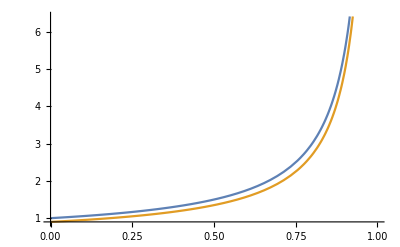

```mathematica
Plot[{Abs[(-1+V-S V)/(-1+V)]/.mH-> 0.05/.S-> 0.5,Abs[((-1+2 mH) (1+(-1+S) V))/(-1+V)]/.mH-> 0.05/.S-> 0.5},{V,0,1}]
```

Leading eigenvalue always independent of migration.

#### Equilibrium 2 – hosts fixed for WT allele, parasites fixed for mutant allele

```mathematica
equi[[2]]
```

{pH[1,t]→0,pH[2,t]→0,pP[1,t]→1,pP[2,t]→1}

```mathematica
JMtrxEqui[2]//MatrixForm
```

(((-1+mH) (-1+V))/(1+(-1+S) V) | (mH-mH V)/(1+(-1+S) V) | 0 | 0
(mH-mH V)/(1+(-1+S) V) | ((-1+mH) (-1+V))/(1+(-1+S) V) | 0 | 0
0 | 0 | (-1+mP)/(-1+S) | mP/(1-S)
0 | 0 | mP/(1-S) | (-1+mP)/(-1+S))

```mathematica
λList[2]
```

{((-1+2 mH) (-1+V))/(1+(-1+S) V),1/(1-S),(1-V)/(1+(-1+S) V),(-1+2 mP)/(-1+S)}

```mathematica
Map[Simplify[#,Assumptions->{mH>0,mP>0,1>S>0,0<V<1}]&,λList[2]]
```

{((-1+2 mH) (-1+V))/(1+(-1+S) V),1/(1-S),(1-V)/(1+(-1+S) V),(-1+2 mP)/(-1+S)}

```mathematica
Map[Reduce[{#>1,mP≥0,mH≥0,1>S>0,0<V<1}]&,λList[2]]//MatrixForm
```

(False
0<S<1&&mP≥0&&0<V<1&&mH≥0
False
0≤mP<1/2&&2 mP<S<1&&0<V<1&&mH≥0)

With some degree of virulence and specificity, always unstable.

```mathematica
Reduce[{1/(1-S)≤ (-1+2 mP)/(-1+S),mH≥0,1>S>0,0<V<1}]
```

mP≤0&&0<S<1&&0<V<1&&mH≥0

Leading eigenvalue never contains term for migration. Migration decreases size of second eigenvalue.

```mathematica
1/(1-S)
1/(1-S)-(2 mP)/(1-S)
```

#### Equilibrium 3 – all polymorphic

```mathematica
equi[[3]]
```

{pH[1,t]→1/2,pH[2,t]→1/2,pP[1,t]→1/2,pP[2,t]→1/2}

```mathematica
JMtrxEqui[3]//MatrixForm
```

(1-mH | mH | ((-1+mH) S V)/(2+(-2+S) V) | -(mH S V)/(2+(-2+S) V)
mH | 1-mH | -(mH S V)/(2+(-2+S) V) | ((-1+mH) S V)/(2+(-2+S) V)
((-1+mP) S)/(-2+S) | (mP S)/(2-S) | 1-mP | mP
(mP S)/(2-S) | ((-1+mP) S)/(-2+S) | mP | 1-mP)

```mathematica
Map[Simplify[#,Assumptions->{mH>0,mP>0,1>S>0,0<V<1}]&,λList[3]]
```

{(-4+4 V+S (2+(-4+S) V)-S √((-2+S) V (2+(-2+S) V)))/((-2+S) (2+(-2+S) V)),(-4+4 V+S (2+(-4+S) V)+S √((-2+S) V (2+(-2+S) V)))/((-2+S) (2+(-2+S) V)),-1/((-2+S) (2+(-2+S) V))(4 (-1+mH+mP) (-1+V)+(-1+mH+mP) S^2 V-2 (-1+mH+mP) S (-1+2 V)+√((-2+S) (2+(-2+S) V) (2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-1+mH+mP)^2 S^2) V))),1/((-2+S) (2+(-2+S) V))(-4 (-1+mH+mP) (-1+V)-(-1+mH+mP) S^2 V+2 (-1+mH+mP) S (-1+2 V)+√((-2+S) (2+(-2+S) V) (2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-1+mH+mP)^2 S^2) V)))}

```mathematica
re=Re[λList[3][[1]]/.{S->0.1,V->0.3,mH->0.0001,mP->0.0001}];
im=Im[λList[3][[1]]/.{S->0.1,V->0.3,mH->0.0001,mP->0.0001}];
Sqrt[re^2+im^2]

re=Re[λList[3][[3]]/.{S->0.1,V->0.3,mH->0.0001,mP->0.0001}];
im=Im[λList[3][[3]]/.{S->0.1,V->0.3,mH->0.0001,mP->0.0001}];
Sqrt[re^2+im^2]
```

1.00055

1.00035

Unstable.

```mathematica
Reduce[{-1/((-2+S) (2+(-2+S) V))(4 (-1+mH+mP) (-1+V)+(-1+mH+mP) S^2 V-2 (-1+mH+mP) S (-1+2 V)+√((-2+S) (2+(-2+S) V) (2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-1+mH+mP)^2 S^2) V)))>1,1>mH>0,1>mP>0,1>S>0,0<V<1}]//FullSimplify
```

(8 mH mP)/(-1+2 mH+2 mP)<S<1&&(8 mH mP (-2+S))/(-16 mH mP+16 mH mP S+(1-2 mH-2 mP) S^2)<V<1&&((0<mH<(1-2 mP)/(2-8 mP)&&1/2<mP<1)||(0<mP<1/6&&(1-2 mP)/(2-8 mP)<mH<1))

```mathematica
D[-1/((-2+S) (2+(-2+S) V))(4 (-1+mH+mP) (-1+V)+(-1+mH+mP) S^2 V-2 (-1+mH+mP) S (-1+2 V)+√((-2+S) (2+(-2+S) V) (2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-1+mH+mP)^2 S^2) V))),mH]//Simplify
```

-(S (2-4 V)+4 (-1+V)+S^2 V+((-2+S) (2+(-2+S) V) (-S^2 V+mH (-2+S) (2+(-2+S) V)+mP (4-2 S-4 V+4 S V+S^2 V)))/(√((-2+S) (2+(-2+S) V) (2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-1+mH+mP)^2 S^2) V))))/((-2+S) (2+(-2+S) V))

```mathematica
Series[-(S (2-4 V)+4 (-1+V)+S^2 V+((-2+S) (2+(-2+S) V) (-S^2 V+mH (-2+S) (2+(-2+S) V)+mP (4-2 S-4 V+4 S V+S^2 V)))/(√((-2+S) (2+(-2+S) V) (2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-1+mH+mP)^2 S^2) V))))/((-2+S) (2+(-2+S) V))/.mH-> ϵ mH/.mP-> mP ϵ,{ϵ,0,1}]
```

(S^2 V-√((-2+S) S^2 V (2-2 V+S V)))/(√((-2+S) S^2 V (2-2 V+S V)))+(2 (2 mH-2 mP-mH S+mP S-2 mH V+2 mP V+2 mH S V-2 mP S V) ϵ)/(√((-2+S) S^2 V (2-2 V+S V)))+O[ϵ]^2

```mathematica
Reduce[{(S^2 V-√((-2+S) S^2 V (2-2 V+S V)))/(√((-2+S) S^2 V (2-2 V+S V)))+(2 (2 mH-2 mP-mH S+mP S-2 mH V+2 mP V+2 mH S V-2 mP S V))/(√((-2+S) S^2 V (2-2 V+S V)))>0,0<S<1,0<V<1}]
```

False

```mathematica
(S^2 V-√((-2+S) S^2 V (2-2 V+S V)))/(√((-2+S) S^2 V (2-2 V+S V)))+(2 (2 mH-2 mP-mH S+mP S-2 mH V+2 mP V+2 mH S V-2 mP S V))/(√((-2+S) S^2 V (2-2 V+S V)))/.mH-> 0.01/.mP-> 0.01/.S-> 0.1/.V-> 0.3
```

-1.-0.0332289 ⅈ

#### Equilibrium 4 – hosts fixed for mutant allele, parasites fixed for WT allele

```mathematica
equi[[4]]
```

{pH[1,t]→1,pH[2,t]→1,pP[1,t]→0,pP[2,t]→0}

```mathematica
JMtrxEqui[4]//MatrixForm
```

(((-1+mH) (-1+V))/(1+(-1+S) V) | (mH-mH V)/(1+(-1+S) V) | 0 | 0
(mH-mH V)/(1+(-1+S) V) | ((-1+mH) (-1+V))/(1+(-1+S) V) | 0 | 0
0 | 0 | (-1+mP)/(-1+S) | mP/(1-S)
0 | 0 | mP/(1-S) | (-1+mP)/(-1+S))

```mathematica
λList[1]
```

{(-1+2 mP) (-1+S),(-1+V-S V)/(-1+V),1-S,((-1+2 mH) (1+(-1+S) V))/(-1+V)}

```mathematica
Map[Simplify[#,Assumptions->{mH>0,mP>0,1>S>0,0<V<1}]&,λList[1]]
```

{(-1+2 mP) (-1+S),(-1+V-S V)/(-1+V),1-S,((-1+2 mH) (1+(-1+S) V))/(-1+V)}

```mathematica
Map[Reduce[{#>1,1≥ mP≥0,1≥ mH≥0,1>S>0,0<V<1}]&,λList[1]]//MatrixForm
```

(False
0≤mP≤1&&0<V<1&&0<S<1&&0≤mH≤1
False
0≤mP≤1&&0<S<1&&0≤mH<1/2&&-(2 mH)/(-2 mH-S+2 mH S)<V<1)

With some degree of virulence and specificity, always unstable.

```mathematica
Map[Reduce[{#<-1,1≥ mP≥0,1≥ mH≥0,1>S>0,0<V<1}]&,λList[1]]//MatrixForm
```

(False
False
False
0≤mP≤1&&0<S<1&&1/2<mH≤1&&(2-2 mH)/(2-2 mH-S+2 mH S)<V<1)

```mathematica
{{Eigenvalue, Conditions, Unique conditions}, {(-1+V-S V)/(-1+V), 0≤mP≤1&&0<V<1&&0<S<1&&0≤mH≤1, 0≤mH≤1,0<V<1}, {((-1+2 mH) (1+(-1+S) V))/(-1+V), 0≤mP≤1&&0<S<1&&1/2<mH≤1&&(2-2 mH)/(2-2 mH-S+2 mH S)<V<1, 1/2<mH≤1,(2-2 mH)/(2-2 mH-S+2 mH S)<V<1}}
```

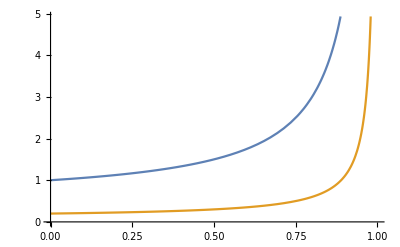

```mathematica
Plot[{Abs[(-1+V-S V)/(-1+V)]/.mH-> 0.6/.S-> 0.5,Abs[((-1+2 mH) (1+(-1+S) V))/(-1+V)]/.mH-> 0.6/.S-> 0.5},{V,0,1}]
```

Leading eigenvalue always independent of migration.

```mathematica
Clear[WH,WP,pH1,pP1,pH2,pP2,equs,equs2,equi]
```

```mathematica
WH[1,u_,t_]:=1-V(X pP[u,t]+Y(1-pP[u,t]))/.Y->(1-X);
WH[2,u_,t_]:=1-V(Y pP[u,t]+X(1-pP[u,t]))/.Y->(1-X) ;
WP[1,u_,t_]:=1+a(X pH[u,t]+Y(1-pH[u,t]))/.Y->(1-X);
WP[2,u_,t_]:=1+a(Y pH[u,t]+X(1-pH[u,t]))/.Y->(1-X);
```

```mathematica
pH1[u_,t_]:=(pH[u,t] WH1[1,u,t])/(pH[u,t]WH1[1,u,t]+(1-pH[u,t])WH1[2,u,t])
pP1[u_,t_]:=(pP[u,t] WP1[1,u,t])/(pP[u,t]WP1[1,u,t]+(1-pP[u,t])WP1[2,u,t])
```

```mathematica
pH2[u_,t_]:=pH1[u,t](1-mH )+mH*pH1[Mod[u,2]+1,t]
pP2[u_,t_]:=pP1[u,t](1-mP)+mP*pP1[Mod[u,2]+1,t]
```

```mathematica
pH2[2,t]/.pH2[1,t]-> 0.5/.pP2[1,t]-> 0.5/.pP2[2,t]-> 0.5/.pH2[2,t]-> 0.5//Simplify
```

0.5

### Individual-Based Simulations

```mathematica
parsN={S-> 0,V->0.2,mH->0.01,mP->0.01,κH->150,κP->150,tMax->300};
parsN2={S-> 0,V->0.2,mH->0.05,mP->0.05,κH->150,κP->150,tMax->300};
parsN3={S-> 0,V->0.2,mH->0.001,mP->0.001,κH->300,κP->150,tMax->300};
parsN4={S->0,V->0.5,a->0.1,mH->0.05,mP->0.05,κH->150,κP->150,tMax->300};
pars1={S-> 0.8,V->0.2,a->0.1,mH->0.01,mP->0.01,κH->150,κP->150,tMax->300};
pars2={S->0.8,V->0.2,a->0.1,mH->0.05,mP->0.05,κH->150,κP->150,tMax->300};
pars3={S->0.8,V->0.2,a->0.1,mH->0.001,mP->0.001,κH->150,κP->150,tMax->300};
pars4={S->0.8,V->0.5,a->0.1,mH->0.05,mP->0.05,κH->150,κP->150,tMax->300};
pars5={S->0.65,V->0.2,a->0.1,mH->0.05,mP->0.05,κH->150,κP->150,tMax->300};
```

Absolute fitness values

```mathematica
WH[1,u_,pVec_]:=pVec[[4-Mod[u,2]]](1-V) +(1-pVec[[4-Mod[u,2]]])S +(1-pVec[[4-Mod[u,2]]])(1-S)(1-V);
WH[2,u_,pVec_]:=(1-pVec[[4-Mod[u,2]]])(1-V)+pVec[[4-Mod[u,2]]]S +pVec[[4-Mod[u,2]]](1-S)(1-V)  ;
WP[1,u_,pVec_]:=pVec[[u]]+(1-pVec[[u]])(1-S);
WP[2,u_,pVec_]:=(1-pVec[[u]])+pVec[[u]](1-S);
```

Relative fitness values

```mathematica
wH[u_,pVec_]:=WH[1,u,pVec]/(pVec[[u]] WH[1,u,pVec]+(1-pVec[[u]])WH[2,u,pVec]) ;
wP[u_,pVec_]:=WP[1,u,pVec]/(pVec[[4-Mod[u,2]]] WP[1,u,pVec]+(1-pVec[[4-Mod[u,2]]])WP[2,u,pVec]) ;
```

```mathematica
Clear[Sim2]
Sim2[pars_,intS_]:=Sim2[pars,intS]=Block[{out,g,nH1s,nP1s,nH2s,nP2s,nMH1,nMH2,nMP1,nMP2,nMH11,nMH12,nMH21,nMH22,nMP11,nMP12,nMP21,nMP22,nH1sm,nH2sm,nP1sm,nP2sm,nH11sm,nH21sm,nH12sm,nH22sm,nP11sm,nP12sm,nP21sm,nP22sm,nH1prime,nH2prime,nP1prime,nP2prime},out={{1/2,1/2,1/2,1/2}}//N;
For[g=1,g≤(tMax/.pars),g++,

(*Selection*)
nH1s=RandomVariate[BinomialDistribution[(κH/.pars),wH[1,out[[-1]]]out[[-1,1]]/.pars]];
nP1s=RandomVariate[BinomialDistribution[(κP/.pars),wP[1,out[[-1]]]out[[-1,3]]/.pars]];
nH2s=RandomVariate[BinomialDistribution[(κH/.pars),wH[2,out[[-1]]]out[[-1,2]]/.pars]];
nP2s=RandomVariate[BinomialDistribution[(κP/.pars),wP[2,out[[-1]]]out[[-1,4]]/.pars]];

(*Number of type 1 host migrants out of population 1*)
nMH11=RandomVariate[BinomialDistribution[nH1s,mH/.pars]];
nMH21=RandomVariate[BinomialDistribution[nH2s,mH/.pars]];

(*Number of type 2 host migrants out of population 1*)
nMH12=RandomVariate[BinomialDistribution[κH-nH1s/.pars,mH/.pars]];
nMH22=RandomVariate[BinomialDistribution[κH-nH2s/.pars,mH/.pars]];

(*Number of type 1 hosts after migration*)
nH11sm=nH1s-nMH11+nMH21;
nH21sm=nH2s-nMH21+nMH11;
 
(*Number of type 2 hosts after migration*)
nH12sm=κH-nH1s-nMH12+nMH22/.pars;
nH22sm=κH-nH2s-nMH22+nMH12/.pars;

(*Number of type 1 parasite migrants out of population 1*)
nMP11=RandomVariate[BinomialDistribution[nP1s,mP/.pars]];
nMP21=RandomVariate[BinomialDistribution[nP2s,mP/.pars]];

(*Number of type 2 parasite migrants out of population 1*)
nMP12=RandomVariate[BinomialDistribution[κP-nP1s/.pars,mP/.pars]];
nMP22=RandomVariate[BinomialDistribution[κP-nP2s/.pars,mP/.pars]];

(*Number of type 1 parasites after migration*)
nP11sm=nP1s-nMP11+nMP21;
nP21sm=nP2s-nMP21+nMP11;
 
(*Number of type 2 hosts after migration*)
nP12sm=κP-nP1s-nMP12+nMP22/.pars;
nP22sm=κP-nP2s-nMP22+nMP12/.pars;

AppendTo[out,{nH11sm/(nH11sm+nH12sm),nH21sm/(nH21sm+nH22sm),nP11sm/(nP11sm+nP12sm),nP21sm/(nP21sm+nP22sm)}/.pars//N]
];
out
]
```

```mathematica
mean[pars_]:=mean[pars]=Mean[Table[2 ((Sim2[pars,j][[;;,1]]+Sim2[pars,j][[;;,2]])/2)(1-(Sim2[pars,j][[;;,1]]+Sim2[pars,j][[;;,2]])/2),{j,1,2000}]]
```

```mathematica
Clear[SD]
SD[pars_]:=SD[pars]=Mean[Table[(2 ((Sim2[pars,j][[;;,1]]+Sim2[pars,j][[;;,2]])/2)(1-(Sim2[pars,j][[;;,1]]+Sim2[pars,j][[;;,2]])/2)-mean[pars])^2,{j,1,2000}]]//Sqrt;
```

```mathematica
Clear[pHDiff,pHDiffSD]
pHDiff[pars_]:=pHDiff[pars]=(mH/.pars)*Mean[Table[Sqrt[(Sim2[pars,j][[;;,1]]-Sim2[pars,j][[;;,2]])^2],{j,1,2000}]]
pHDiffSD[pars_]:=pHDiffSD[pars]=Mean[Table[(Sqrt[((mH/.pars)*Sim2[pars,j][[;;,1]]-(mH/.pars)*Sim2[pars,j][[;;,2]])^2]-pHDiff[pars])^2,{j,1,2000}]]//Sqrt;
```

```mathematica
leg=LineLegend[{Directive[Orange,Opacity[0.3]],Directive[Red,Opacity[0.3]],Directive[Blue,Opacity[0.3]],Directive[Orange],Directive[Red],Directive[Blue]},{"Neutral, m_i=0.001","Neutral, m_i=0.01","Neutral, m_i=0.05","Coevolutionary, m_i=0.001","Coevolutionary, m_i=0.01","Coevolutionary, m_i=0.05"}];
```

```mathematica
g=Show[ListLinePlot[{mean[parsN],mean[parsN]+(2SD[parsN])/Sqrt[2000],mean[parsN]-(2SD[parsN])/Sqrt[2000]},PlotStyle->Directive[Red,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.1]]}}}],
ListLinePlot[{mean[parsN2],mean[parsN2]+(2SD[parsN2])/Sqrt[2000],mean[parsN2]-(2SD[parsN2])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.1]]}}}],
ListLinePlot[{mean[parsN3],mean[parsN3]+(2SD[parsN3])/Sqrt[2000],mean[parsN3]-(2SD[parsN3])/Sqrt[2000]},PlotStyle->Directive[Orange,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Orange,Opacity[0.1]]}}}],
ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[2000],mean[pars2]-(2SD[pars2])/Sqrt[2000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],ListLinePlot[{mean[pars3],mean[pars3]+(2SD[pars3])/Sqrt[2000],mean[pars3]-(2SD[pars3])/Sqrt[2000]},PlotStyle->Directive[Orange],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
PlotRange-> {0,0.5},Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False];
```

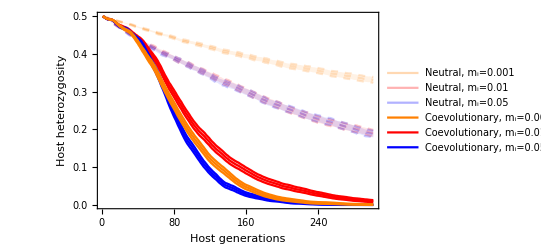

```mathematica
gLegend=Legended[g,leg]
```

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Migration.png",gLegend,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Migration.png

```mathematica
leg2=LineLegend[{Directive[Blue,Opacity[0.2],Dashed],Directive[Blue,Opacity[0.4]],Directive[Blue]},{"Neutral, m_i=0.05","Coevolutionary, m_i=0.05, S=0.65","Coevolutionary, m_i=0.05, S=0.8"}]
```

```mathematica
g1=Show[
ListLinePlot[{mean[parsN2],mean[parsN2]+(2SD[parsN2])/Sqrt[2000],mean[parsN2]-(2SD[parsN2])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.1]]}}}],
ListLinePlot[{mean[pars5],mean[pars5]+(2SD[pars5])/Sqrt[2000],mean[pars5]-(2SD[pars5])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.4]],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[2000],mean[pars2]-(2SD[pars2])/Sqrt[2000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
PlotRange-> {0,0.5},Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False];
g1Legend=Legended[g1,leg2];
```

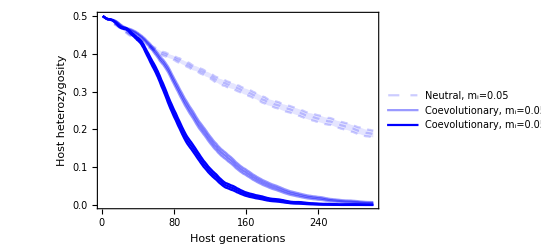

```mathematica
g1Legend
```

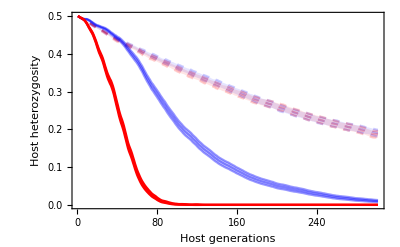

```mathematica
leg3=LineLegend[{Directive[Blue,Opacity[0.2],Dashed],Directive[Red,Opacity[0.2],Dashed],Directive[Blue],Directive[Red]},{"Neutral, m_i=0.05, V=0.2","Neutral, m_i=0.05, V=0.5","Coevolutionary, m_i=0.05, V=0.2","Coevolutionary, m_i=0.05, V=0.5"}]
g2=Show[
ListLinePlot[{mean[parsN],mean[parsN]+(2SD[parsN])/Sqrt[2000],mean[parsN]-(2SD[parsN])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.1]]}}}],
ListLinePlot[{mean[parsN4],mean[parsN4]+(2SD[parsN4])/Sqrt[2000],mean[parsN4]-(2SD[parsN4])/Sqrt[2000]},PlotStyle->Directive[Red,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.1]]}}}],

ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.4]],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars4],mean[pars4]+(2SD[pars4])/Sqrt[2000],mean[pars4]-(2SD[pars4])/Sqrt[2000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}},PlotRange-> All],
PlotRange-> All,Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False]
```

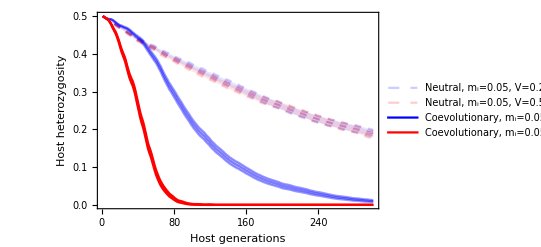

```mathematica
g2Legend=Legended[g2,leg3]
```

```mathematica
g12Legend=GraphicsColumn[{g1Legend,g2Legend}]
```

-Graphics-

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Specificity.png",g1Legend,"PNG",ImageResolution-> 300]
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Virulence.png",g2Legend,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Specificity.png

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Virulence.png